```mathematica
(*Definisci i valori di m e n*)
nQubs=6;
jj=2^(nQubs-1);
mm=2;
nn=3;

(*Definizione della funzione*)
f[m_,n_,phi_]:=Piecewise[{
{Exp[I*(-m*phi+n*(phi+3*Pi/2))],0<=phi<Pi/2},
{Exp[I*(-m*phi+n*(phi+      Pi/2))],Pi/2<=phi<Pi},
{Exp[I*(-m*phi+n*(phi-      Pi/2))],Pi<=phi<3*Pi/2},
{Exp[I*(-m*phi+n*(phi-3*Pi/2))],3*Pi/2<=phi<=2*Pi}}]

integrale=NIntegrate[f[mm, nn, phi],{phi,0,2*Pi}];

integrale/(2*Pi)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.46945×10^-17+4.16334×10^-17 ⅈ and 9.89295×10^-16 for the integral and error estimates.

-5.5218×10^-18+6.62616×10^-18 ⅈ

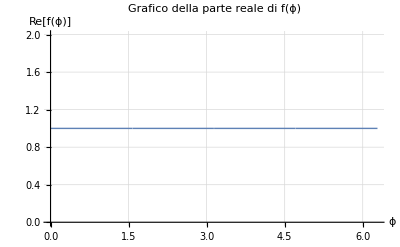

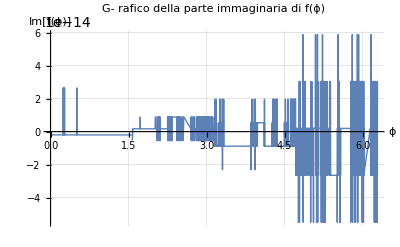

```mathematica
(*Plot delle componenti reale e immaginaria*)
(*Traccia il grafico della parte reale di f(phi)*)
Plot[Re[f[mm, nn, phi]],{phi,0,2*Pi},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ϕ","Re[f(ϕ)]"},PlotLabel->"Grafico della parte reale di f(ϕ)",GridLines->Automatic]

(*Traccia il grafico della parte immaginaria di f(phi)*)
Plot[Im[f[mm, nn, phi]],{phi,0,2*Pi},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ϕ","Im[f(ϕ)]"},PlotLabel->"G-
rafico della parte immaginaria di f(ϕ)",GridLines->Automatic]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {4.58957}. NIntegrate obtained -9.88792×10^-16-4.04191×10^-16 ⅈ and 8.78417×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {5.14181}. NIntegrate obtained -5.46438×10^-16-1.45717×10^-16 ⅈ and 9.16849×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained -6.245×10^-16+2.77556×10^-16 ⅈ and 1.36755×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.46945×10^-17+4.16334×10^-17 ⅈ and 9.89295×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.46945×10^-17+4.16334×10^-17 ⅈ and 9.89295×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.93889×10^-18-5.55112×10^-17 ⅈ and 9.89444×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

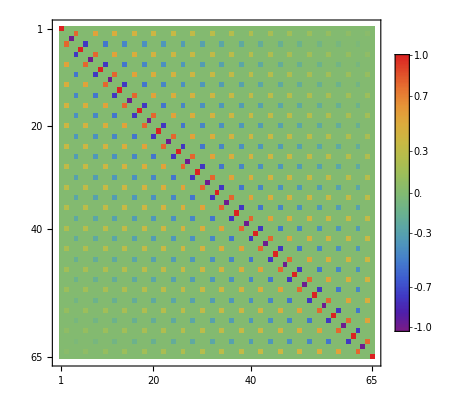

```mathematica
(*Calcolo della matrice di integrali in theta*)
ttt=Table[Table[NIntegrate[f[mm,nn,φ],{φ,0,2π}],{mm,-jj,jj}]/(2π),{nn,-jj,jj}];

ttt=ttt//Chop;

MatrixPlot[ttt,ColorFunction->"Rainbow",PlotLegends->BarLegend["Rainbow"]]
```

```mathematica
(*Normalized Legendre associated polynomial function*)
LGP[j_,m_,theta_]:=Sqrt[(2 j+1)/(4 Pi) (j-m)!/(j+m)!] LegendreP[j,m,Cos[theta]]

(*Calcolo della matrice di integrali in theta*)
tttTheta=Table[Table[NIntegrate[LGP[jj,mm,θ]LGP[jj,nn,θ],{θ,0,π}],{mm,-jj,jj}],{nn,-jj,jj}];

tttTheta=tttTheta//Chop;

p = "done"
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.6996}. NIntegrate obtained -2.34188×10^-17 and 3.29655×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.6996}. NIntegrate obtained -1.21431×10^-17 and 3.20232×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.6996}. NIntegrate obtained 8.67362×10^-18 and 2.65749×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

done

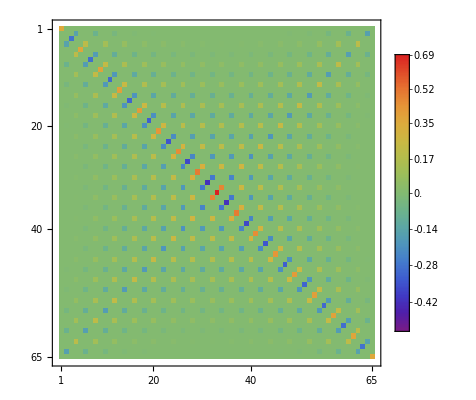

```mathematica
(*Moltiplicazione elemento per elemento*)
tttProduct=tttTheta*ttt;

tttProduct=tttProduct//Chop;

MatrixPlot[tttProduct,ColorFunction->"Rainbow",PlotLegends->BarLegend["Rainbow"]]
```

```mathematica
(*Definisci i valori di m e n*)
nQubs=6;
jj=2^(nQubs-1);
mm=2;
nn=3;

(*Definizione della funzione*)
f[m_,n_,phi_]:=Piecewise[{
{Exp[I*(-m*phi+n*(phi+3*Pi/2))],0<=phi<Pi/2},
{Exp[I*(-m*phi+n*(phi+      Pi/2))],Pi/2<=phi<Pi},
{Exp[I*(-m*phi+n*(phi-      Pi/2))],Pi<=phi<3*Pi/2},
{Exp[I*(-m*phi+n*(phi-3*Pi/2))],3*Pi/2<=phi<=2*Pi}}]

integrale=NIntegrate[f[mm, nn, phi],{phi,0, 2*Pi}];

integrale
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.46945×10^-17+4.16334×10^-17 ⅈ and 9.89295×10^-16 for the integral and error estimates.

-3.46945×10^-17+4.16334×10^-17 ⅈ